```mathematica
CIso[Ei_,nu_] := {{1/Ei, -nu/Ei, 0},{-nu/Ei, 1/Ei, 0}, {0, 0, (2 * (1 + nu))/Ei}};
```

```mathematica
EIso[Ei_,nu_] := Simplify[Inverse[CIso[Ei,nu]]];
```

```mathematica
COrtho[Ex_, Ey_, nuYX_, mu_] := {{1/Ex, -nuYX/Ey, 0}, {-nuYX/Ey, 1/Ey, 0}, {0, 0, 1/mu}};
```

```mathematica
EOrtho[Ex_, Ey_, nuYX_, mu_] := Simplify[Inverse[COrtho[Ex, Ey, nuYX, mu]]];
```

```mathematica
Manipulate[Plot3D[Norm[EIso[Ei, ν] - EIso[ETarget,vTarget], "Frobenius"], {Ei, 5, 295},{ν, -0.4, 0.8}, AxesLabel->{ν,E,diff}, ImageSize->Full, PlotRange->{Automatic,Automatic,{0,400}}, PerformanceGoal->"Quality"], {{ETarget, 100}, 5, 295}, {{vTarget, .3}, -.4, 0.8}]
```

```mathematica
FrobDist[EVar_,vVar_, ETarget_, vTarget_]:=Norm[EIso[EVar, vVar] - EIso[ETarget,vTarget], "Frobenius"]^2;
```

```mathematica
mE = Manipulate[minE=FindMinimum[FrobDist[EVar, vVar, ETarget, vTarget], EVar, AccuracyGoal->1, PrecisionGoal->1];pt={EVar, minE[[1]]} /. minE[[2]]; Show[Plot[FrobDist[EVar,vVar, ETarget, vTarget], {EVar, 5, 295}, PlotRange->{Automatic, {0, 2000}}, AxesLabel->{"E"}, ImageSize->Large,PerformanceGoal->"Quality",PlotLabel->"Elasticity Tensor Distance Frobenius Norm vs. Young's Modulus\n(Target E = "<>ToString[ETarget]<>", Target ν = "<>ToString[vTarget]<>", ν = "<>ToString[vVar]<>")\nMinimum distance "<>ToString[minE[[1]]]<>" at  E: "<>ToString[EVar/.minE[[2]]]],Graphics[{Red, PointSize[Large], Point[pt]}]],
	{{ETarget, 150, "Target E"},5,295}, {{vTarget, 0.3, "Target ν"}, -.4, 0.75},  {{vVar, 0.3, "ν"}, -.4, 0.75}]
```

```mathematica
{EVar, FrobDist[EVar, 0.3, 150, 0.37]} /. testMin[[2]]
```

{160.193,17.9272}

```mathematica
mE = Manipulate[Plot[FrobDist[EVar, vVar,ETarget,vTarget], {vVar, -.4, .75}, PlotRange->{Automatic, {0, 2000}}, AxesLabel->{"ν"}, ImageSize->Full, PlotLabel->"Elasticity Tensor Distance Frobenius Norm vs. Poisson Ratio\n(Target E = "<>ToString[ETarget]<>", Target ν = "<>ToString[vTarget]<>", E = "<>ToString[EVar]<>")",PerformanceGoal->"Quality"],
	{{ETarget, 150, "Target E"},5,295}, {{vTarget, 0.3, "Target ν"}, -.4, 0.75},  {{EVar, 150, "E"}, 5, 295}]
```

```mathematica
Simplify[Norm[{{1/(1-ν^2),ν/(1-ν^2),0},{ν/(1-ν^2),1/(1-ν^2),0},{0,0,1/(2+2 ν)}}, "Frobenius"]^2, ν ∈ Reals]
```

(9-2 ν+9 ν^2)/(4 (-1+ν^2)^2)

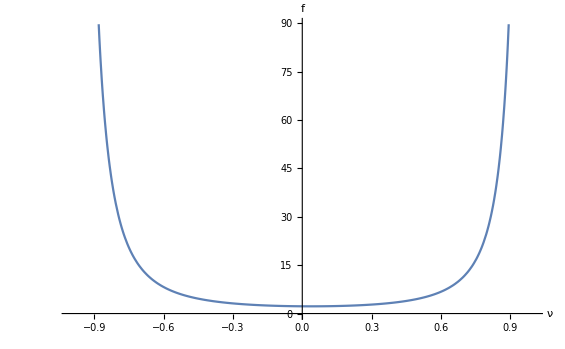

```mathematica
fPlot = Plot[(9-2 ν+9 ν^2)/(4 (-1+ν^2)^2), {ν, -1, 1}, AxesLabel->{ν,f}]
```

```mathematica
Export["quadraticCoefficient.pdf",fPlot]
```

quadraticCoefficient.pdf

```mathematica
Simplify[FrobDist[1, ν, 1,νTarget]]
```

Abs[1/(2+2 ν)-1/(2+2 νTarget)]^2+2 (Abs[1/(1-ν^2)+1/(-1+νTarget^2)]^2+Abs[ν/(1-ν^2)+νTarget/(-1+νTarget^2)]^2)

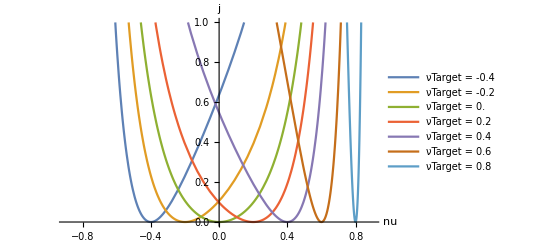

```mathematica
vPlot = Plot[Evaluate[Table[FrobDist[1,ν,1,νTarget],{νTarget, -.4, 0.8, 0.2}]], {ν, -.9,0.9}, PlotRange->{Automatic,{0,1}}, PlotLegends->Table["νTarget = "<>ToString[νTarget], {νTarget, -.4, 0.8, 0.2}], AxesLabel->{nu,j}]
```

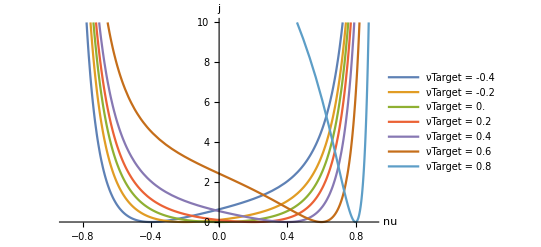

```mathematica
vPlotZoomOut = Plot[Evaluate[Table[FrobDist[1,ν,1,νTarget],{νTarget, -.4, 0.8, 0.2}]], {ν, -.9,0.9}, PlotRange->{Automatic,{0,10}}, PlotLegends->Table["νTarget = "<>ToString[νTarget], {νTarget, -.4, 0.8, 0.2}], AxesLabel->{nu,j}]
```

```mathematica
Export["vPlot.pdf",vPlot]; Export["vPlotZoomOut.pdf",vPlotZoomOut];
```

```mathematica
(1/(2+2 ν)-1/(2+2 νTarget))^2+2 (1/(1-ν^2)-1/(1-νTarget^2))^2+2 (ν/(1-ν^2)-νTarget/(1-νTarget^2))^2
```

(1/(2+2 ν)-1/(2+2 νTarget))^2+2 (1/(1-ν^2)-1/(1-νTarget^2))^2+2 (ν/(1-ν^2)-νTarget/(1-νTarget^2))^2

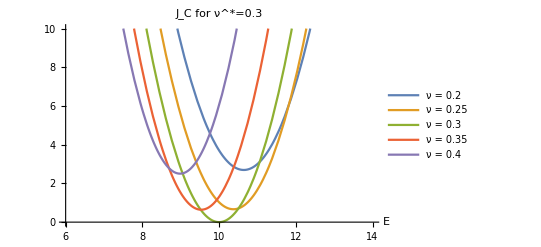

```mathematica
target = 0.3;
interplayE = Plot[Evaluate[Table[FrobDist[Ei,ν,10,target],{ν, target-.1, target+.1, 0.05}]], {Ei, 6,14},PlotRange->{Automatic,{0,10}}, PlotLegends->Table["ν = "<>ToString[ν], {ν, target-.1, target+.1, 0.05}], AxesLabel->{"E"}, PlotLabel->"J_C for ν^*="<>ToString[target]]
```

```mathematica
Export["interplayE.pdf", interplayE];
```